```mathematica
SetDirectory[Last[Sort[SetDirectory["~/java/exp"];FileNames[RegularExpression["\\d*_\\d*"]]]]];
```

```mathematica
data=ToExpression@StringSplit[Import[Sequence@@FileNames["*_O_GENOMES_MATH.txt"]],"\n"];
```

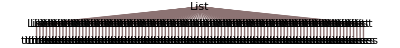
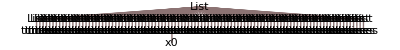
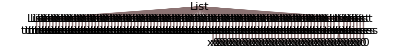

```mathematica
TreeForm/@data
```

```mathematica
DeleteDuplicates/@data
```

{{{times}},{{times},{times[x0]}},{{times},{times[x0]},{times[x0,x0]}}}